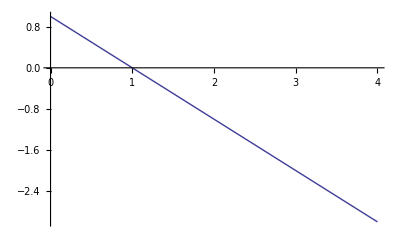

{{t→1}}

```mathematica
Subscript[p, g]={0,0,0};(*plane*)
Subscript[n, g]=Normalize[{0,1,0}];(*normal*)
p={0,2,0};(*sphere position*)
u={0,-1,0};(*velocity*)
r=1;(*radius*)
f=(p+u t-Subscript[p, g]).Subscript[n, g]-r==0;(*signed distance to plane*)
Plot[f,{t,0,4}]
Solve[f,t]
```